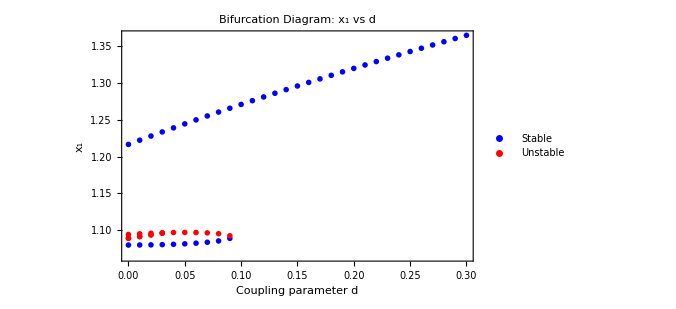

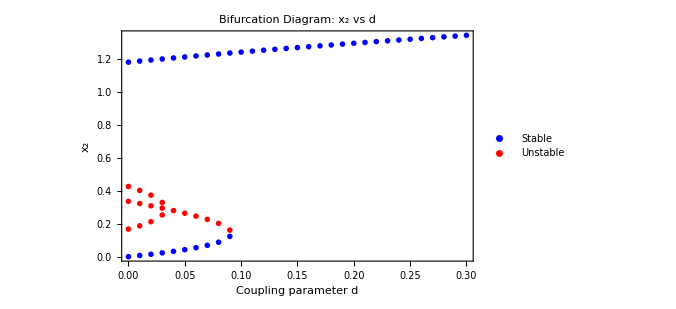

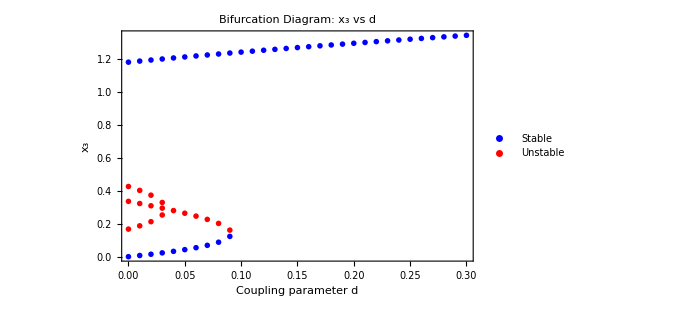

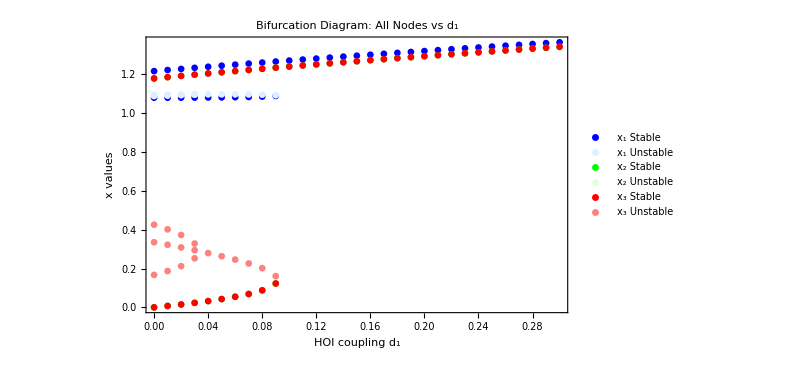

```mathematica
ClearAll["Global`*"]


aVal=4;bVal=1;d1Val=0.2;
dRange=Range[0.0,0.3,0.01];
vars={x1,x2,x3};


f1=-a*(x1-0.5)^3+b*(x1-0.5)+0.2+d*(x2+x3)+d1*(2*x2*x3);
f2=-a*(x2-0.5)^3+b*(x2-0.5)+d*(x1+x3)+d1*(2*x1*x3) ;
f3=-a*(x3-0.5)^3+b*(x3-0.5)+d*(x1+x2)+d1*(2*x1*x2);
F={f1,f2,f3};


J=D[F,{vars}];


eqs=Thread[F==0];


stablePtsX1={};unstablePtsX1={};
stablePtsX2={};unstablePtsX2={};
stablePtsX3={};unstablePtsX3={};


Do[params={a->aVal,b->bVal,d->dVal,d1->d1Val};
sols=Quiet[Solve[eqs/. params,vars,Reals]];

If[ListQ[sols]&&sols=!={},Do[point=N[vars/. s,20];
If[VectorQ[point,NumericQ]&&AllTrue[point,Im[#]==0&],Jval=N[J/. params/. Thread[vars->point],20];
If[MatrixQ[Jval,NumericQ],eigs=Eigenvalues[Jval];

(*Check stability*)isStable=AllTrue[Re[eigs],#<0&];
If[isStable,AppendTo[stablePtsX1,{dVal,point[[1]]}];
AppendTo[stablePtsX2,{dVal,point[[2]]}];
AppendTo[stablePtsX3,{dVal,point[[3]]}],AppendTo[unstablePtsX1,{dVal,point[[1]]}];
AppendTo[unstablePtsX2,{dVal,point[[2]]}];
AppendTo[unstablePtsX3,{dVal,point[[3]]}]]]],{s,sols}]];,{dVal,dRange}];

(*Plot x1*)
plotX1=If[Length[stablePtsX1]>0||Length[unstablePtsX1]>0,ListPlot[{If[Length[stablePtsX1]>0,Style[stablePtsX1,Blue,PointSize[0.008]],Nothing],If[Length[unstablePtsX1]>0,Style[unstablePtsX1,Red,PointSize[0.008]],Nothing]},Frame->True,FrameLabel->{"Coupling parameter d","x₁"},PlotRange->All,Joined->False,PlotLegends->{"Stable","Unstable"},PlotLabel->"Bifurcation Diagram: x₁ vs d",ImageSize->500],Graphics[Text["No valid points for x₁"]]];

(*Plot x2*)
plotX2=If[Length[stablePtsX2]>0||Length[unstablePtsX2]>0,ListPlot[{If[Length[stablePtsX2]>0,Style[stablePtsX2,Blue,PointSize[0.008]],Nothing],If[Length[unstablePtsX2]>0,Style[unstablePtsX2,Red,PointSize[0.008]],Nothing]},Frame->True,FrameLabel->{"Coupling parameter d","x₂"},PlotRange->All,Joined->False,PlotLegends->{"Stable","Unstable"},PlotLabel->"Bifurcation Diagram: x₂ vs d",ImageSize->500],Graphics[Text["No valid points for x₂"]]];

(*Plot x3*)
plotX3=If[Length[stablePtsX3]>0||Length[unstablePtsX3]>0,ListPlot[{If[Length[stablePtsX3]>0,Style[stablePtsX3,Blue,PointSize[0.008]],Nothing],If[Length[unstablePtsX3]>0,Style[unstablePtsX3,Red,PointSize[0.008]],Nothing]},Frame->True,FrameLabel->{"Coupling parameter d","x₃"},PlotRange->All,Joined->False,PlotLegends->{"Stable","Unstable"},PlotLabel->"Bifurcation Diagram: x₃ vs d",ImageSize->500],Graphics[Text["No valid points for x₃"]]];

(*Display all plots*)
Print[plotX1];
Print[plotX2];
Print[plotX3];
combinedPlot=ListPlot[{Style[stablePtsX1,Blue,PointSize[0.008]],Style[unstablePtsX1,LightBlue,PointSize[0.008]],Style[stablePtsX2,Green,PointSize[0.008]],Style[unstablePtsX2,LightGreen,PointSize[0.008]],Style[stablePtsX3,Red,PointSize[0.008]],Style[unstablePtsX3,Pink,PointSize[0.008]]},Frame->True,FrameLabel->{"HOI coupling d₁","x values"},PlotLabel->"Bifurcation Diagram: All Nodes vs d₁",PlotLegends->{"x₁ Stable","x₁ Unstable","x₂ Stable","x₂ Unstable","x₃ Stable","x₃ Unstable"},Joined->False,PlotRange->All,ImageSize->600];

Print[combinedPlot];
```